## Setup

```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"challenge\\Sample3\\"]];
```

```mathematica
imrows={1,512};
imcols={1,512};
subset=59;
```

### Import

```mathematica
namelist = {"Sample3 Reference","Sample3-001 X0.10 Y0.10 N2 C0 R0","Sample3-002 X0.20 Y0.20 N2 C0 R0","Sample3-003 X0.30 Y0.30 N2 C0 R0","Sample3-004 X0.40 Y0.40 N2 C0 R0","Sample3-005 X0.50 Y0.50 N2 C0 R0","Sample3-006 X0.60 Y0.60 N2 C0 R0","Sample3-007 X0.70 Y0.70 N2 C0 R0","Sample3-008 X0.80 Y0.80 N2 C0 R0","Sample3-009 X0.90 Y0.90 N2 C0 R0","Sample3-010 X1.00 Y1.00 N2 C0 R0"};
imlist=Table[Import[StringJoin[namelist[[ii]],".tif"],"Image"],{ii,Dimensions[namelist][[1]]}];
matlist=Table[Import[StringJoin[namelist[[ii]],".mat"],"LabeledData"],{ii,1,Dimensions[namelist][[1]]}];
```

```mathematica
imref=imlist[[1]];
imdefs=imlist[[2;;]];
numdefs=Dimensions[imdefs][[1]]
```

10

```mathematica
imsize=ImageDimensions[imref];
flowsize={imcols[[2]]-imcols[[1]]+1,imrows[[2]]-imrows[[1]]+1};
imcenter={Mean[imcols],imsize[[2]]-Mean[imrows]};
imbottomleft={imcols[[1]],imrows[[2]]};
```

#### Compute dense optical flow; default MaxIternations = 10

```mathematica
flow=Table[{0,0},{flowsize[[1]]},{flowsize[[2]]}];
```

```mathematica
dispvals = Table[ImageDisplacements[{ImageTake[imref,imrows,imcols],ImageTake[imdefs[[ii]],imrows,imcols]},MaxIterations->10],{ii,numdefs}];
```

```mathematica
Dimensions[dispvals]
```

{10,1,512,512,2}

## Separate the displacement components

#### Extract the data framed by one subset width from the array border

```mathematica
u1=Table[dispvals[[ii,;;,;;,;;,1]][[1,(subset+1);;-(subset+1),(subset+1);;-(subset-1)]],{ii,numdefs}];
u2=Table[dispvals[[ii,;;,;;,;;,2]][[1,(subset+1);;-(subset+1),(subset+1);;-(subset-1)]],{ii,numdefs}];
Dimensions[u1]
```

{10,394,396}

## Stats comparison

```mathematica
vicu=Table[matlist[[ii+1,5,2]][[(subset+1);;-(subset+1),(subset+1);;-(subset-1)]],{ii,numdefs}];
vicv=Table[matlist[[ii+1,6,2]][[(subset+1);;-(subset+1),(subset+1);;-(subset-1)]],{ii,numdefs}];
```

```mathematica
Dimensions[vicu]
```

{10,393,395}

```mathematica
Dimensions[vicu]
```

{10,393,395}

```mathematica
vics=Table[Sqrt[vicu[[ii]]^2+vicv[[ii]]^2],{ii,numdefs}];
maths=Table[Sqrt[u1[[ii]]^2+u2[[ii]]^2],{ii,numdefs}];
```

```mathematica
vicsRMSE=Table[RootMeanSquare[Flatten[vics[[ii]]-Sqrt[2]*ii/10]],{ii,numdefs}]
```

{0.00253256,0.00208918,0.00209605,0.00226107,0.00220134,0.0022008,0.0020194,0.00203516,0.00197752,0.0020945}

```mathematica
mathsRMSE=Table[RootMeanSquare[Flatten[maths[[ii]]-Sqrt[2]*ii/10]],{ii,numdefs}]
```

{0.0201826,0.0243026,0.0269766,0.0283934,0.0295863,0.0283701,0.0264801,0.0240014,0.0198821,0.0169565}

```mathematica
vicsRMSEu=Table[RootMeanSquare[Flatten[vicu[[ii]]-ii/10]],{ii,numdefs}];
vicsRMSEv=Table[RootMeanSquare[Flatten[vicv[[ii]]-ii/10]],{ii,numdefs}];
mathsRMSEu=Table[RootMeanSquare[Flatten[u1[[ii]]-ii/10]],{ii,numdefs}];
mathsRMSEv=Table[RootMeanSquare[Flatten[u2[[ii]]-ii/10]],{ii,numdefs}];
```

```mathematica
pxvals=Table[Sqrt[2]*ii/10,{ii,numdefs}]//N
```

{0.141421,0.282843,0.424264,0.565685,0.707107,0.848528,0.989949,1.13137,1.27279,1.41421}

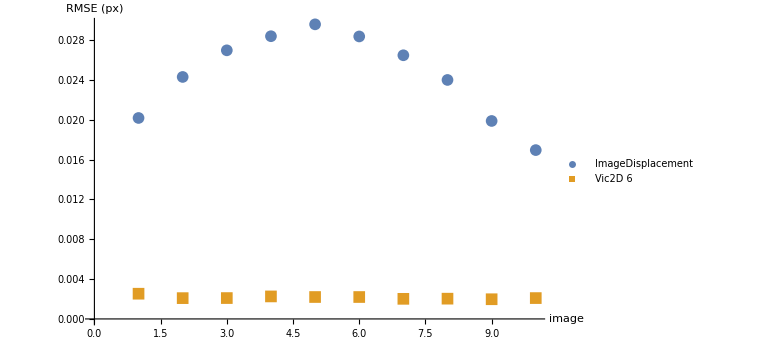

```mathematica
complp=ListPlot[{mathsRMSE,vicsRMSE},PlotLegends->Placed[{"ImageDisplacement","Vic2D 6"},Bottom],AxesLabel->{"image","RMSE (px)"},ImageSize->Large,BaseStyle->{FontSize->14},PlotMarkers->{Automatic,12}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["complp.pdf",complp];
Export["complp.png",complp];
```